#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-27);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v24/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v24/results

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);


evv=Eigenvalues[evm=(Transpose[invtrafma].norm).invtrafma];
Print["Min[Re] = ",Min[Re[evv]]];
Print["Max[Im] = ",Max[Im[evv]]];
evm=Chop[evm,10^(-6)];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}]

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

N_final = {312}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

J=0.5:  E_0=-1.3318

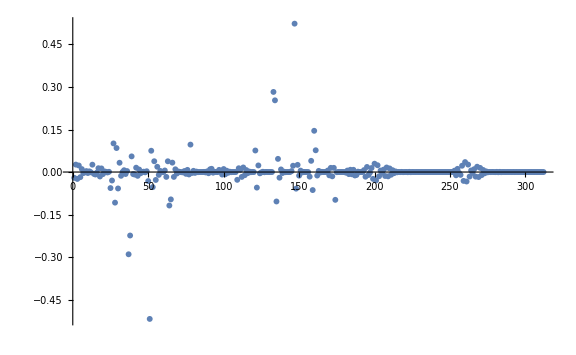
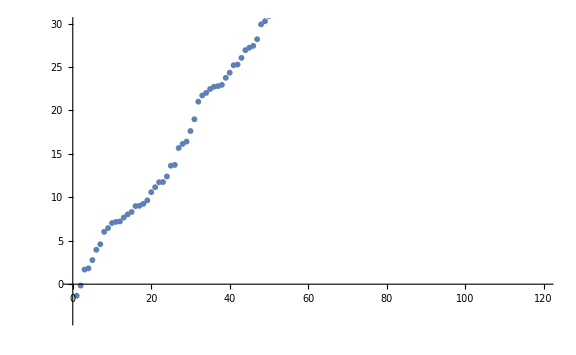
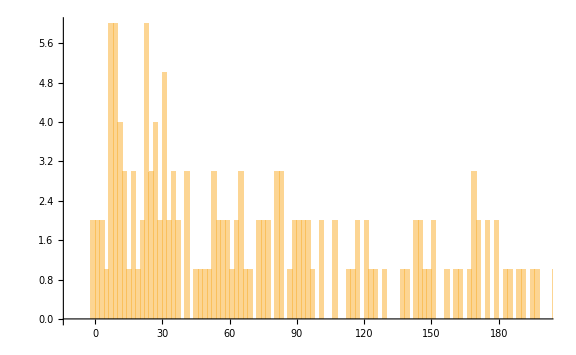
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
orderedEVbareOut=Sort[Transpose[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVbareOut[[1,1]];v0l=orderedEVbareOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,v0l];
AppendTo[LitEigSys,orderedEVbareOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,120},{-4,30}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in Norm-Eigen-Vector Basis

Final-state Basis dimension = {312}

min/max: {3.36556×10^-9,4.00041×10^8}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

Min[Re] = 0.116719

Max[Im] = 8.15785×10^-11

J=0.5:  E_0=-1.3318

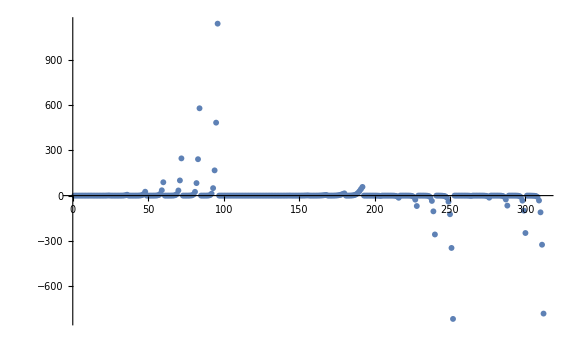
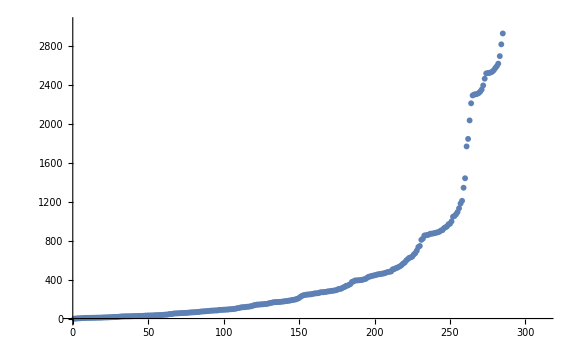
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitEigSys={};
fullv0l={};
dE=2.;
Do[
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[1]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
orderedEVSYOut=Sort[Transpose[Eigensystem[{tst=(Transpose[LitNmhi].LitHam[[nj]]).LitNmhi;tst=(tst+Transpose[tst])/2,Transpose[LitNmhi].LitNorm[[nj]].LitNmhi}]],Re[#1[[1]]]<Re[#2[[1]]]&];

e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,LitNmh.v0l];
AppendTo[LitEigSys,orderedEVSYOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];

Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,Automatic},{-4,Automatic}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```